```mathematica
x = Import["/home/tim/laboratorij/biclustering/test/distribution_data.txt","List"]
```

{0.323281,0.00109719,0.38119,0.306067,0.281793,0.718201,0.0867179,0.200655,0.0119508,0.174152,0.217746,0.386596,99976,0.410599,0.18347,0.15262,0.703959,0.442698,0.430426,0.214464,0.274812,0.38026,0.324202,0.34538,0.0683186}
 |  |  |  |

```mathematica
x
```

{0.323281,0.00109719,0.38119,0.306067,0.281793,0.718201,0.0867179,0.200655,0.0119508,0.174152,0.217746,0.386596,0.302685,0.15627,0.266102,0.328445,0.061341,0.263127,99964,0.38657,0.101121,0.239649,0.11636,0.29595,0.160682,0.410599,0.18347,0.15262,0.703959,0.442698,0.430426,0.214464,0.274812,0.38026,0.324202,0.34538,0.0683186}
 |  |  |  |

```mathematica
FindDistribution[x, 3]
```

{BetaDistribution[1.50601,4.71801],WeibullDistribution[1.55815,0.26859],MixtureDistribution[{0.363368,0.636632},{NormalDistribution[0.109293,0.0576254],NormalDistribution[0.318735,0.137982]}]}

```mathematica
{BetaDistribution[1.5060124100554981,4.718008925988233],WeibullDistribution[1.5581500813224383,0.26858973671298314],MixtureDistribution[{0.363367817907853,0.6366321820921469},{NormalDistribution[0.10929345233838964,0.05762539335011533],NormalDistribution[0.3187354456889553,0.13798198134859926]}]}
```

```mathematica
n = 20
```

20

```mathematica
n* NIntegrate[y * (1 - y) ^(4.71801 - 1) * y ^(1.50601 - 1)/Beta[1.50601, 4.71801]*((1 - BetaRegularized[y, 1.50601, 4.71801]) ^ (n- 1)), {y, 0, 1}]
```

0.0314415

```mathematica
PDF[BetaDistribution[a,b], y]
```

Piecewise[{{((1-y)^(-1+b) y^(-1+a))/Beta[a,b], 0<y<1}, {0, True}}]

```mathematica
CDF[BetaDistribution[a, b], y]
```

Piecewise[{{BetaRegularized[y,a,b], 0<y<1}, {1, y≥1}, {0, True}}]

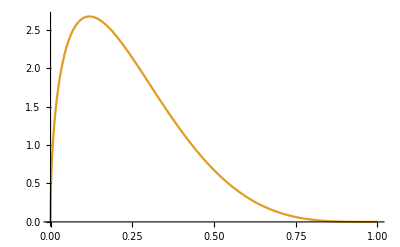

```mathematica
Plot[{PDF[x],PDF[BetaDistribution[1.5, 4.7],y]},{y,0,1}]
```